```mathematica
ρint[x_,T_]=(x^(1/2)(x+2/T)^(1/2)(x+1/T)^2)/(Exp[x+1/T]+1);
ρintp[x_,T_]=D[ρint[x,T], T];
pint[x_,T_]=(x^(3/2)(x+2/T)^(3/2))/(Exp[x+1/T]+1);
pintp[x_,T_]=D[pint[x,T], T];
```

```mathematica
gSM=106.75;
gDM=2 2;
```

```mathematica
ρ[T_]:=π^2/30 gSM T^4+T^4/(2 π^2)NIntegrate[ρint[x,T],{x,0,1000}]gDM
ρp[T_]:=π^2/30 gSM 4 T^3+ 4 T^3/(2 π^2)NIntegrate[ρint[x,T],{x,0,1000}]gDM+T^4/(2 π^2)NIntegrate[ρintp[x,T],{x,0,1000}]gDM
p[T_]:=1/3 π^2/30 gSM T^4+T^4/(6 π^2)NIntegrate[pint[x,T],{x,0,1000}]gDM
pp[T_]:=1/3 π^2/30 gSM 4 T^3+4 T^3/(6 π^2)NIntegrate[pint[x,T],{x,0,1000}]gDM+T^4/(6 π^2)NIntegrate[pintp[x,T],{x,0,1000}]gDM
w[T_]:=p[T]/ρ[T]
cs2[T_]:=pp[T]/ρp[T]
```

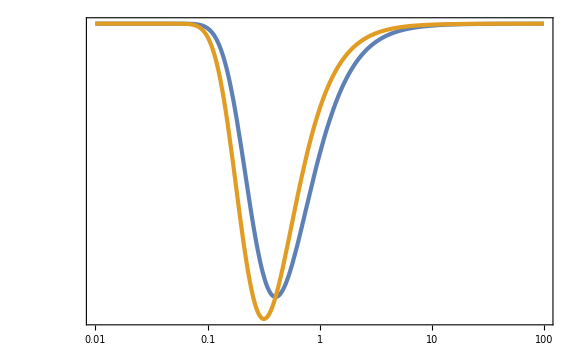

```mathematica
LogLogPlot[{w[T],cs2[T]},{T,0.01,100}]
```